# Empty Blocks

Empty blocks have no BTC transactions and contain only 1 transaction, the block subsidy coinbase transaction.

## Recent empty blocks

```mathematica
Clear["Global`"];
server="localhost";
db=DatabaseReference[
<| "Backend" ->"PostgreSQL"
, "Name"->"bitcoin"
, "Port"-> Automatic
, "Host"->server
,"Username"->"rpc"
,"Password"->"YOURPASSWORD"|>
];
```

```mathematica
ExternalEvaluate[db,
"select height, to_timestamp(time) as time, txs
from blockstats
where txs=1
order by height desc
limit 100;
"
]
```

## Empty blocks by halving

How has empty block frequency changed with time?

```mathematica
emptiesByHalving=ExternalEvaluate[db,
"with subsidyblocks as (select subsidy, count(*) from blockstats group by 1),
     empty as (
select b.subsidy, count(b.*)
from blockstats b
where b.txs = 1
group by 1)
select e.*, s.count as blocks, (e.count::real/s.count::real) as proportion
from empty e
join subsidyblocks s on s.subsidy = e.subsidy
order by e.subsidy desc;
"
]
```

```mathematica
Association[subsidy->#subsidy,count->#count,blocks->#blocks, proportion->PercentForm[#proportion]]&/@(emptiesByHalving //Normal)
```

{<|subsidy→50.,count→83864,blocks→210000,proportion→39.94%|>,<|subsidy→25.,count→3472,blocks→210000,proportion→1.653%|>,<|subsidy→12.5,count→1562,blocks→210000,proportion→0.7438%|>,<|subsidy→6.25,count→734,blocks→210000,proportion→0.3495%|>,<|subsidy→3.125,count→31,blocks→5578,proportion→0.5558%|>}

## Empty block apparition times

```mathematica
emptiesdiff = ExternalEvaluate[db,
"with prior as (select height, time from blockstats)
select b.height, to_timestamp(b.time) as time, txs, b.time - p.time as diff
from blockstats b
join prior p on p.height = b.height - 1
where totalfee = 0
order by b.height desc
limit 1000"
]
```

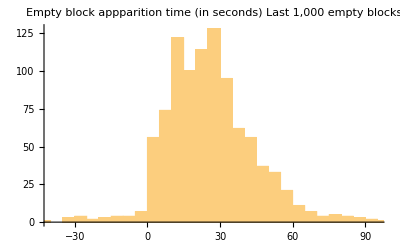

```mathematica
Histogram[
#diff& /@ emptiesdiff
,PlotLabel->"Empty block appparition time (in seconds)\nLast 1,000 empty blocks"
, PlotRange->Automatic
]
```

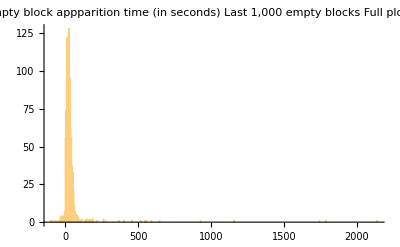

```mathematica
Histogram[
#diff& /@ emptiesdiff
,PlotLabel->"Empty block appparition time (in seconds)\nLast 1,000 empty blocks\nFull plot range"
, PlotRange->Full
]
```